# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Schlick

```mathematica
pSchlick[u_,k_]:=1/(4 Pi)((1-k^2)/(1+k u)^2)
```

### Normalization condition

```mathematica
Integrate[2 Pi pSchlick[u,k],{u,-1,1},Assumptions->-1<k<1]
```

1

### Mean-cosine

```mathematica
Integrate[2 Pi pSchlick[u,k]u,{u,-1,1},Assumptions->-1<k<1]
```

-(k-ArcTanh[k]+k^2 ArcTanh[k])/k^2

### Legendre expansion coefficients

```mathematica
Integrate[2 Pi (2k+1)pSchlick[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi},Assumptions->-1<e<1]
```

ConditionalExpression[1,e≠0]

```mathematica
Integrate[2 Pi (2k+1)pSchlick[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi},Assumptions->-1<e<1]
```

ConditionalExpression[-(3 (e+(-1+e^2) ArcTanh[e]))/e^2,e≠0]

```mathematica
Integrate[2 Pi (2k+1)pSchlick[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi},Assumptions->-1<e<1]
```

ConditionalExpression[-(5 (-6 e+4 e^3-6 (-1+e^2) ArcTanh[e]))/(2 e^3),e≠0]

```mathematica
Integrate[2 Pi (2k+1)pSchlick[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi},Assumptions->-1<e<1]
```

ConditionalExpression[-(7 (30 e-26 e^3-6 (5-6 e^2+e^4) ArcTanh[e]))/(4 e^4),e≠0]

### sampling

```mathematica
cdf=Integrate[2 Pi pSchlick[u,e],{u,-1,x},Assumptions->-1<e<1&&0<x<1]
```

((1+e) (1+x))/(2+2 e x)

```mathematica
Solve[cdf==k,x]
```

{{x→(1+e-2 k)/(-1-e+2 e k)}}

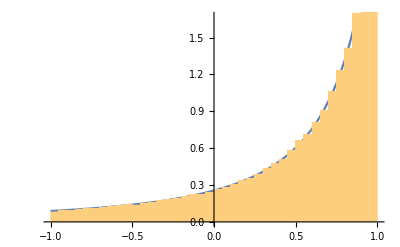

```mathematica
With[{e=-.7},
Show[
Plot[2 Pi pSchlick[u,e],{u,-1,1}],
Histogram[Map[(1+e-2 #)/(-1-e+2 e #)&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
]
```